## 座標関数の定義

```mathematica
catcurvx[t_]:=
(2337Cos[t])/8-(43Cos[2t])/5+(322Cos[3t])/5-(117Cos[4t])/5-(26Cos[5t])/5-(23Cos[6t])/3+(143Cos[7t])/4-(11Cos[8t])/4-(31Cos[9t])/3-(13Cos[10t])/4-(9Cos[11t])/2+(41Cos[12t])/20+8Cos[13t]+(2Cos[14t])/3+6Cos[15t]+(17Cos[16t])/4-(3Cos[17t])/2-(29Cos[18t])/10+(11Cos[19t])/6+(12Cos[20t])/5+(3Cos[21t])/2+(11Cos[22t])/12-(4Cos[23t])/5+Cos[24t]+(17Cos[25t])/8-(7Cos[26t])/2-(5Cos[27t])/6-(11Cos[28t])/10+Cos[29t]/2-Cos[30t]/5-(721Sin[t])/4+(196Sin[2t])/3-(86Sin[3t])/3-(131Sin[4t])/2+(477Sin[5t])/14+27Sin[6t]-(29Sin[7t])/2+(68Sin[8t])/5+Sin[9t]/10+(23Sin[10t])/4-(19Sin[12t])/2-(85Sin[13t])/21+(2Sin[14t])/3+(27Sin[15t])/5+(7Sin[16t])/4+(17Sin[17t])/9-4Sin[18t]-Sin[19t]/2+Sin[20t]/6+(6Sin[21t])/7-Sin[22t]/8+Sin[23t]/3+(3Sin[24t])/2+(13Sin[25t])/5+Sin[26t]-2Sin[27t]+(3Sin[28t])/5-Sin[29t]/5+Sin[30t]/5
```

```mathematica
catcurvy[t_]:=-(125Cos[t])/2-(521Cos[2t])/9-(359Cos[3t])/3+(47Cos[4t])/3-(33Cos[5t])/2-(5Cos[6t])/4+(31Cos[7t])/8+(9Cos[8t])/10-(119Cos[9t])/4-(17Cos[10t])/2+(22Cos[11t])/3+(15Cos[12t])/4-(5Cos[13t])/2+(19Cos[14t])/6+(7Cos[15t])/4+(31Cos[16t])/4-Cos[17t]+(11Cos[18t])/10-(2Cos[19t])/3+(13Cos[20t])/3-(5Cos[21t])/4+(2Cos[22t])/3+Cos[23t]/4+(5Cos[24t])/6+(3Cos[26t])/4-Cos[27t]/2-Cos[28t]/10-Cos[29t]/3-Cos[30t]/19-(637Sin[t])/2-(188Sin[2t])/5-(11Sin[3t])/7-(12Sin[4t])/5+(11Sin[5t])/3-(37Sin[6t])/4+(8Sin[7t])/3+(65Sin[8t])/6-(32Sin[9t])/5-(41Sin[10t])/4-(38Sin[11t])/3-(47Sin[12t])/8+(5Sin[13t])/4-(41Sin[14t])/7-(7Sin[15t])/3-(13Sin[16t])/7+(17Sin[17t])/4-(9Sin[18t])/4+(8Sin[19t])/9+(3Sin[20t])/5-(2Sin[21t])/5+(4Sin[22t])/3+Sin[23t]/3+(3Sin[24t])/5-(3Sin[25t])/5+(6Sin[26t])/5-Sin[27t]/5+(10Sin[28t])/9+Sin[29t]/3-(3Sin[30t])/4
```

## プロット

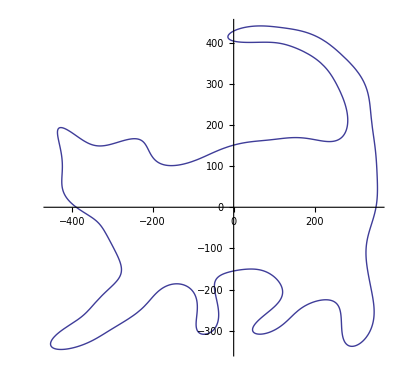

```mathematica
ParametricPlot[{catcurvx[t],catcurvy[t]},{t,0,2Pi}]
```

## 線形変換しよう

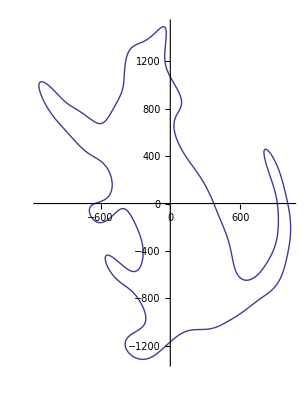

```mathematica
ParametricPlot[{{1,2},{-3,1}}.{catcurvx[t],catcurvy[t]},{t,0,2Pi}]
```

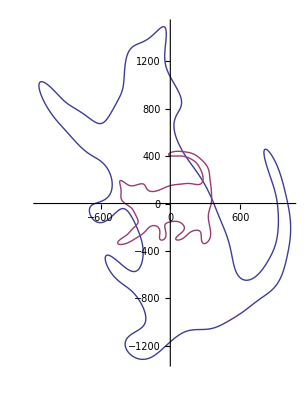

```mathematica
ParametricPlot[{{{1,2},{-3,1}}.{catcurvx[t],catcurvy[t]},{catcurvx[t],catcurvy[t]}},{t,0,2Pi}]
```

### 拡大・縮小

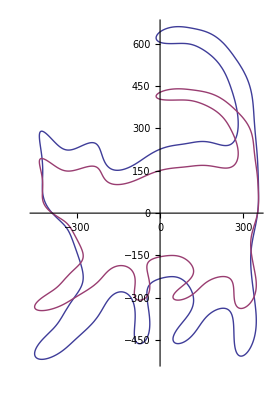

```mathematica
ParametricPlot[{{{1,0},{0,3/2}}.{catcurvx[t],catcurvy[t]},{catcurvx[t],catcurvy[t]}},{t,0,2Pi}]
```

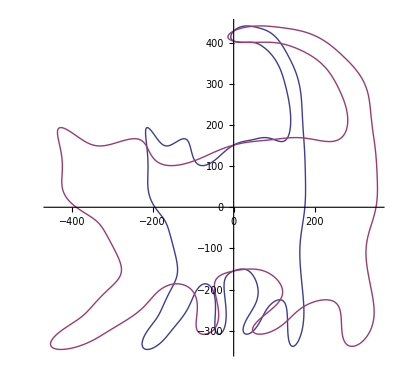

```mathematica
ParametricPlot[{{{1/2,0},{0,1}}.{catcurvx[t],catcurvy[t]},{catcurvx[t],catcurvy[t]}},{t,0,2Pi}]
```

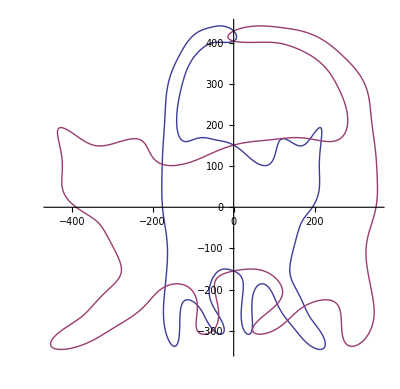

```mathematica
ParametricPlot[{{{-1/2,0},{0,1}}.{catcurvx[t],catcurvy[t]},{catcurvx[t],catcurvy[t]}},{t,0,2Pi}]
```

### せん断（横ずれ，縦ずれ）

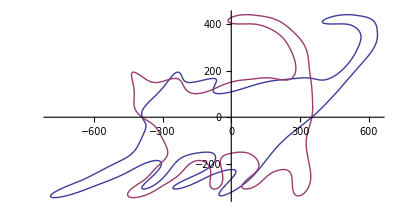

```mathematica
ParametricPlot[{{{1,1},{0,1}}.{catcurvx[t],catcurvy[t]},{catcurvx[t],catcurvy[t]}},{t,0,2Pi}]
```

```mathematica
ParametricPlot[{{{1,0},{2,1}}.{catcurvx[t],catcurvy[t]},{catcurvx[t],catcurvy[t]}},{t,0,2Pi}]
```

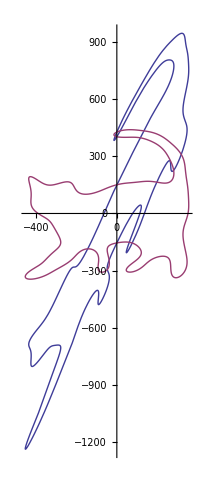

### 回転

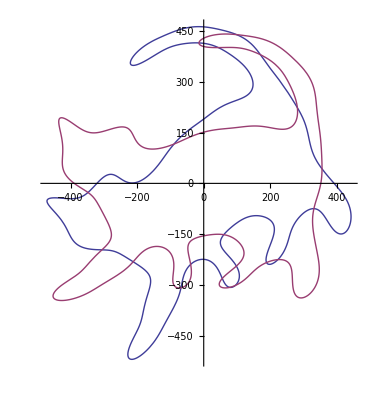

```mathematica
ParametricPlot[{{{Cos[Pi/6],-Sin[Pi/6]},{Sin[Pi/6],Cos[Pi/6]}}.{catcurvx[t],catcurvy[t]},{catcurvx[t],catcurvy[t]}},{t,0,2Pi}]
```

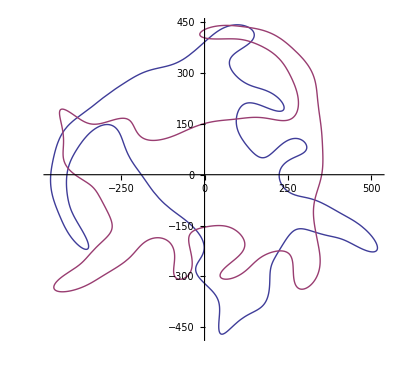

```mathematica
ParametricPlot[{{{Cos[2Pi/3],-Sin[2Pi/3]},{Sin[2Pi/3],Cos[2Pi/3]}}.{catcurvx[t],catcurvy[t]},{catcurvx[t],catcurvy[t]}},{t,0,2Pi}]
```

### 対称移動

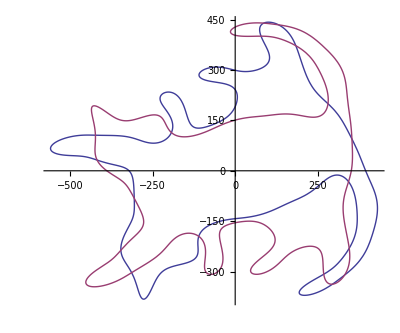

```mathematica
ParametricPlot[{{{Cos[Pi/6],Sin[Pi/6]},{Sin[Pi/6],-Cos[Pi/6]}}.{catcurvx[t],catcurvy[t]},{catcurvx[t],catcurvy[t]}},{t,0,2Pi}]
```

```mathematica
ー
```

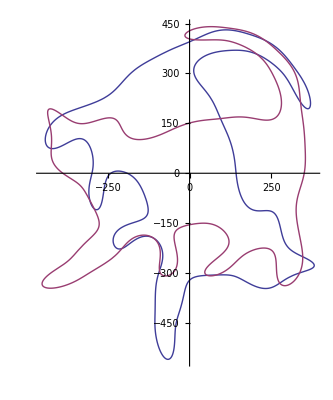

```mathematica
ParametricPlot[{{{Cos[2Pi/3],Sin[2Pi/3]},{Sin[2Pi/3],-Cos[2Pi/3]}}.{catcurvx[t],catcurvy[t]},{catcurvx[t],catcurvy[t]}},{t,0,2Pi}]
```